# Wolfram Quantum Framework Live Coding Demo

```mathematica
2+2
```

4

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

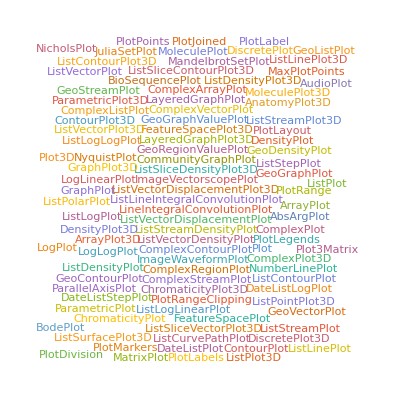

```mathematica
Names["*Plot*"]//WordCloud
```

### WQF

Documentation:

```mathematica
SystemOpen@"https://wolfr.am/wolfram-quantum"
```

Install:

```mathematica
PacletInstall["https://wolfr.am/DevWQCF",ForceVersionInstall->True]
```

PacletObject[…]

Load:

```mathematica
<<Wolfram`QuantumFramework`
```

```mathematica
Names["Quantum*"]//Column
```

QuantumBasis
QuantumBeamSearch
QuantumChannel
QuantumCircuitOperator
QuantumDistance
QuantumEntangledQ
QuantumEntanglementMonotone
QuantumMeasurement
QuantumMeasurementOperator
QuantumOperator
QuantumPartialTrace
QuantumState
QuantumTensorProduct
QuantumWignerTransform

Finite Discrete Hilbert Space

#### QuantumBasis

```mathematica
QuantumBasis[]
```

QuantumBasis[…]

```mathematica
QuantumBasis["PauliX"]
```

QuantumBasis[…]

```mathematica
QuantumBasis[]["Properties"]//Short
```

{Association,ConjugateTranspose,Diagram,Dimension,«65»,TensorRepresentation,Transpose,Type}

```mathematica
Normal/@QuantumBasis[]["Association"]
```

<|0→{1,0},1→{0,1}|>

```mathematica
Table[Normal/@QuantumBasis[b]["Association"],{b,{"X","Y","Z"}}]//Column
```

<|ψ_(x_-)→{-1/(√2),1/(√2)},ψ_(x_+)→{1/(√2),1/(√2)}|>
<|ψ_(y_-)→{ⅈ/(√2),1/(√2)},ψ_(y_+)→{-ⅈ/(√2),1/(√2)}|>
<|ψ_(z_-)→{0,1},ψ_(z_+)→{1,0}|>

```mathematica
Normal/@QuantumBasis[<|"up"->{-1,1},"down"->{a,b}|>]["Association"]
```

<|up→{-1,1},down→{a,b}|>

```mathematica
QuantumBasis["Computational"]==QuantumBasis[]==QuantumBasis[2]
```

True

```mathematica
QuantumBasis[9]
```

QuantumBasis[…]

```mathematica
QuantumBasis[{3,3}]
```

QuantumBasis[…]

#### QuantumState

```mathematica
QuantumState[]
```

QuantumState[…]

```mathematica
QuantumState[]//TraditionalForm
```

0

Cmd+Shift+T - traditional form

```mathematica
QuantumState[]
```

0

```mathematica
QuantumState[]["Dagger"]
```

0

```mathematica
QuantumState[{a,b}]
```

QuantumState[…]

```mathematica
QuantumState[{a,b}]["Amplitudes"]
```

<|0→a,1→b|>

```mathematica
QuantumState[{a,b}]
```

a 0+b 1

```mathematica
Head[a]
```

Symbol

```mathematica
QuantumState[{a,b,2}]
```

a 00+b 01+2 10

```mathematica
QuantumState[{a,b,2}]["Qudits"]
```

2

```mathematica
QuantumState[{a,b,2}]["Dimensions"]
```

{2,2}

```mathematica
QuantumState[{a,b,2},3]
```

QuantumState[…]

```mathematica
QuantumState[{a,b,2},3]
```

a 0+b 1+2 2

```mathematica
QuantumState[{a,b,2}]==QuantumState[{a,b,2,0}]
```

True

```mathematica
QuantumState[{a,b}]+QuantumState[{c,d}]
```

(a+c) 0+(b+d) 1

```mathematica
x QuantumState[{a,b}]+y QuantumState[{c,d}]
```

(a x+c y) 0+(b x+d y) 1

```mathematica
QuantumState[{a,b}]["Properties"]
```

{Amplitudes,Association,Basis,Bend,BendDual,Bipartition,BlochCartesianCoordinates,BlochPlot,BlochSphericalCoordinates,Computational,Conjugate,ConjugateTranspose,Decompose,DensityMatrix,Diagram,Dimension,Dimensions,Disentangle,Double,Dual,Eigenstates,Eigenvalues,Eigenvectors,ElementAssociation,ElementDimension,ElementDimensions,ElementNames,Elements,Entropy,FinalParameters,Formula,HasInputQ,InitialParameters,Input,InputBasis,InputDimension,InputDimensions,InputElementDimension,InputElementDimensions,InputElementNames,InputElements,InputMatrix,InputNameDimension,InputNameDimensions,InputQudits,InputRank,InputSize,InputTensor,Kind,Label,LabelHead,Matrix,MatrixDimensions,MatrixElementDimensions,MatrixNameDimensions,MatrixRepresentation,MatrixState,Mixed,MixedStateQ,NameDimensions,Names,Norm,NormalElementNames,NormalizedAmplitudes,NormalizedDensityMatrix,NormalizedOperator,NormalizedProjector,NormalizedQ,NormalizedState,NormalizedStateVector,Operator,OrthogonalElements,Output,OutputBasis,OutputDimension,OutputDimensions,OutputElementDimension,OutputElementDimensions,OutputElementNames,OutputElements,OutputMatrix,OutputNameDimension,OutputNameDimensions,OutputQudits,OutputRank,OutputSize,OutputTensor,ParameterArity,Parameters,ParameterSpec,Picture,PrimeBasis,Probabilities,Projector,Projectors,Pure,PureEffects,PureMaps,PureStateQ,PureStates,Purify,Purity,QuditBasis,Qudits,Rank,Reverse,ReverseInput,ReverseOutput,SchmidtBasis,Simplify,Size,SpectralBasis,State,StateMatrix,StateTensor,StateType,StateVector,Tensor,TensorDimensions,TensorRepresentation,Trace,TraceNorm,Transpose,Type,Unbend,Unpurify,VectorState,VonNeumannEntropy,Weights}

```mathematica
QuantumState[{a,b}]["SchmidtBasis"]
```

√(a Conjugate[a]+b Conjugate[b]) u_1 v_1

```mathematica
Normal/@QuantumState[{"RandomPure",2}]["SchmidtBasis"]["Association"]
```

<|u_1 v_1→{{0.460028+0.358207 ⅈ,0.0332433+0.118095 ⅈ},{-0.716277-0.323433 ⅈ,-0.0809986-0.144179 ⅈ}},u_1 v_2→{{-0.0973291-0.07469 ⅈ,0.161938+0.560102 ⅈ},{0.151197+0.0669926 ⅈ,-0.389757-0.68246 ⅈ}},u_2 v_1→{{-0.620097-0.482847 ⅈ,-0.0448105-0.159187 ⅈ},{-0.531381-0.239943 ⅈ,-0.06009-0.106961 ⅈ}},u_2 v_2→{{0.131195+0.100679 ⅈ,-0.218286-0.754992 ⅈ},{0.112167+0.0496994 ⅈ,-0.289147-0.506293 ⅈ}}|>

```mathematica
Normal/@QuantumState[{"RandomPure",3}]["SchmidtBasis"]["Association"]
```

<|u_1 v_1→{{0.0765949+0.0250698 ⅈ,0.00904566+0.101924 ⅈ,-0.023628+0.14004 ⅈ,-0.138206-0.0476945 ⅈ},{-0.261234-0.190451 ⅈ,0.0916241-0.400101 ⅈ,0.263469-0.505105 ⅈ,0.46832+0.353028 ⅈ}},u_1 v_2→{{-0.0578073-0.130282 ⅈ,0.015429-0.134138 ⅈ,-0.0846487+0.10894 ⅈ,-0.0211272-0.0220189 ⅈ},{0.0593376+0.568655 ⅈ,-0.224879+0.492729 ⅈ,0.457814-0.310918 ⅈ,0.0533639+0.110164 ⅈ}},u_1 v_3→{{-0.0944245+0.125308 ⅈ,0.101214+0.00597754 ⅈ,-0.102578+0.0343704 ⅈ,-0.00384087+0.109061 ⅈ},{0.515372-0.361274 ⅈ,-0.378803-0.14807 ⅈ,0.433939-0.00419722 ⅈ,0.149627-0.411385 ⅈ}},u_1 v_4→{{0.0344777+0.0767686 ⅈ,-0.00925708-0.13944 ⅈ,0.00790929-0.0868429 ⅈ,-0.155343-0.0127838 ⅈ},{-0.0365474-0.335592 ⅈ,-0.137248+0.543514 ⅈ,-0.137655+0.321575 ⅈ,0.576916+0.241029 ⅈ}},u_2 v_1→{{0.307249+0.100564 ⅈ,0.0362853+0.408851 ⅈ,-0.0947802+0.56175 ⅈ,-0.554391-0.191319 ⅈ},{0.0651238+0.047478 ⅈ,-0.0228412+0.0997422 ⅈ,-0.0656808+0.125919 ⅈ,-0.116749-0.0880072 ⅈ}},u_2 v_2→{{-0.231885-0.522608 ⅈ,0.0618911-0.538073 ⅈ,-0.339556+0.436996 ⅈ,-0.0847485-0.0883256 ⅈ},{-0.0147924-0.141762 ⅈ,0.0560606-0.122834 ⅈ,-0.11413+0.0775095 ⅈ,-0.0133032-0.027463 ⅈ}},u_2 v_3→{{-0.37877+0.502653 ⅈ,0.406006+0.023978 ⅈ,-0.411475+0.137872 ⅈ,-0.0154071+0.43748 ⅈ},{-0.128478+0.0900629 ⅈ,0.0944327+0.0369128 ⅈ,-0.108178+0.00104634 ⅈ,-0.037301+0.102555 ⅈ}},u_2 v_4→{{0.138302+0.307946 ⅈ,-0.0371334-0.559344 ⅈ,0.0317269-0.348357 ⅈ,-0.623135-0.0512801 ⅈ},{0.009111+0.0836607 ⅈ,0.0342149-0.135494 ⅈ,0.0343164-0.0801663 ⅈ,-0.143821-0.0600868 ⅈ}}|>

```mathematica
QuantumState[{{a,b},{c,d}}]
```

QuantumState[…]

```mathematica
QuantumState[{{1,0},{0,-1}}]["DensityMatrix"]//MatrixForm
```

(1 | 0
0 | -1)

```mathematica
QuantumState[{{1,0},{0,1}}]
```

QuantumState[…]

```mathematica
QuantumState[RandomReal[1,{2,2}]]
```

QuantumState[…]

```mathematica
QuantumState["RandomMixed"]
```

QuantumState[…]

```mathematica
QuantumState[{"RandomMixed",2},3]
```

QuantumState[…]

```mathematica
state=QuantumState[{"RandomMixed",2},3]
```

QuantumState[…]

```mathematica
state["Purify"]
```

QuantumState[…]

```mathematica
QuantumPartialTrace[state["Purify"],{3,4}]==state==state["Purify"]["Unpurify"]
```

True

```mathematica
state=QuantumState["RandomPure",6]
```

QuantumState[…]

```mathematica
state["Bipartition"]
```

QuantumState[…]

```mathematica
state["Bipartition",2]
```

QuantumState[…]

```mathematica
state["Bipartition",2]["Transpose",{2}]
```

QuantumState[…]

```mathematica
state["Properties"]
```

{Amplitudes,Association,Basis,Bend,BendDual,Bipartition,Computational,Conjugate,ConjugateTranspose,Decompose,DensityMatrix,Diagram,Dimension,Dimensions,Disentangle,Double,Dual,Eigenstates,Eigenvalues,Eigenvectors,ElementAssociation,ElementDimension,ElementDimensions,ElementNames,Elements,Entropy,FinalParameters,Formula,HasInputQ,InitialParameters,Input,InputBasis,InputDimension,InputDimensions,InputElementDimension,InputElementDimensions,InputElementNames,InputElements,InputMatrix,InputNameDimension,InputNameDimensions,InputQudits,InputRank,InputSize,InputTensor,Kind,Label,LabelHead,Matrix,MatrixDimensions,MatrixElementDimensions,MatrixNameDimensions,MatrixRepresentation,MatrixState,Mixed,MixedStateQ,NameDimensions,Names,Norm,NormalElementNames,NormalizedAmplitudes,NormalizedDensityMatrix,NormalizedOperator,NormalizedProjector,NormalizedQ,NormalizedState,NormalizedStateVector,Operator,OrthogonalElements,Output,OutputBasis,OutputDimension,OutputDimensions,OutputElementDimension,OutputElementDimensions,OutputElementNames,OutputElements,OutputMatrix,OutputNameDimension,OutputNameDimensions,OutputQudits,OutputRank,OutputSize,OutputTensor,ParameterArity,Parameters,ParameterSpec,Picture,PrimeBasis,Probabilities,Projector,Projectors,Pure,PureEffects,PureMaps,PureStateQ,PureStates,Purify,Purity,QuditBasis,Qudits,Rank,Reverse,ReverseInput,ReverseOutput,SchmidtBasis,Simplify,Size,SpectralBasis,State,StateMatrix,StateTensor,StateType,StateVector,Tensor,TensorDimensions,TensorRepresentation,Trace,TraceNorm,Transpose,Type,Unbend,Unpurify,VectorState,VonNeumannEntropy,Weights}

```mathematica
QuantumState["RandomMixed"]["BlochPlot"]
```

-Graphics3D-

```mathematica
QuantumState["Plus","X"]
```

ψ_(x_+)

```mathematica
QuantumState["Plus","X"]==QuantumState["Plus","X"]
```

True

```mathematica
QuantumState[QuantumState["Plus","X"],"Y"]
```

(1/2-ⅈ/2) ψ_(y_-)+(1/2+ⅈ/2) ψ_(y_+)

```mathematica
QuantumState[QuantumState["Plus","X"],"Y"]==QuantumState["Plus"]
```

True

#### QuantumOperator

```mathematica
QuantumState["+"]["Operator"]
```

QuantumOperator[…]

```mathematica
QuantumState["+"]["Operator"]
```

00/2+01/2+10/2+11/2

```mathematica
QuantumOperator[{{1,2},{3,4}}]
```

00+2 01+3 10+4 11

```mathematica
QuantumOperator[{{1,2,3},{3,4,5}}]
```

000+2 001+3 010+3 011+4 100+5 101

```mathematica
QuantumOperator["Fourier"]
```

QuantumOperator[…]

```mathematica
QuantumOperator[{"Fourier",3}]
```

00/(√3)+01/(√3)+02/(√3)+10/(√3)+(ⅇ^((2 ⅈ π)/3) 11)/(√3)+(ⅇ^(-(2 ⅈ π)/3) 12)/(√3)+20/(√3)+(ⅇ^(-(2 ⅈ π)/3) 21)/(√3)+(ⅇ^((2 ⅈ π)/3) 22)/(√3)

```mathematica
QuantumOperator["Fourier"]==QuantumOperator["H"]
```

True

```mathematica
QuantumOperator["Fourier"][QuantumState["0"]]
```

QuantumState[…]

```mathematica
f@x
```

f[x]

```mathematica
QuantumOperator["Fourier"]@QuantumState["0"]
```

QuantumState[…]

```mathematica
QuantumOperator["Fourier"]@QuantumState["0"]
```

0/(√2)+1/(√2)

```mathematica
QuantumOperator["Fourier"]@QuantumState["RandomPure"]
```

(0.518125+0.681656 ⅈ) 0-(0.187272+0.0875983 ⅈ) 1

```mathematica
QuantumOperator["H"]
```

QuantumOperator[…]

```mathematica
QuantumOperator["H",{5}]
```

QuantumOperator[…]

```mathematica
QuantumCircuitOperator@QuantumOperator["H",{5}]
```

-Graphics-

```mathematica
QuantumCircuitOperator@QuantumOperator["CNOT"]
```

QuantumCircuitOperator[…]

```mathematica
QuantumCircuitOperator@QuantumOperator[{"Controlled","NOT",{2}}]
```

QuantumCircuitOperator[…]

```mathematica
QuantumCircuitOperator@QuantumOperator["CNOT",{2,1}]
```

QuantumCircuitOperator[…]

```mathematica
QuantumOperator["RandomUnitary"]["Properties"]
```

{Amplitudes,Arity,Association,Basis,Bend,BendDual,Bipartition,Computational,Conjugate,ConjugateTranspose,ControlOrder,Dagger,Decompose,DensityMatrix,Diagram,Dimension,Dimensions,Disentangle,Double,Dual,Eigenstates,Eigensystem,Eigenvalues,Eigenvectors,ElementAssociation,ElementDimension,ElementDimensions,ElementNames,Elements,Entropy,FinalParameters,FirstInputQudit,FirstOutputQudit,Formula,FullArity,FullInputOrder,FullOrder,FullOutputOrder,HasInputQ,HermitianQ,InitialParameters,Input,InputBasis,InputDimension,InputDimensions,InputElementDimension,InputElementDimensions,InputElementNames,InputElements,InputMatrix,InputNameDimension,InputNameDimensions,InputOrder,InputOrderQuditMapping,InputQuditOrder,InputQudits,InputRank,InputSize,InputTensor,Kind,Label,LabelHead,LastInputQudit,LastOutputQudit,Matrix,MatrixDimensions,MatrixElementDimensions,MatrixNameDimensions,MatrixRepresentation,MatrixState,MaxArity,Mixed,MixedStateQ,NameDimensions,Names,Norm,NormalElementNames,NormalizedAmplitudes,NormalizedDensityMatrix,NormalizedOperator,NormalizedProjector,NormalizedQ,NormalizedState,NormalizedStateVector,Operator,Order,Ordered,OrderedInput,OrderedMatrix,OrderedMatrixRepresentation,OrderedOutput,OrderedTensor,OrderedTensorRepresentation,OrthogonalElements,Output,OutputBasis,OutputDimension,OutputDimensions,OutputElementDimension,OutputElementDimensions,OutputElementNames,OutputElements,OutputMatrix,OutputNameDimension,OutputNameDimensions,OutputOrder,OutputOrderQuditMapping,OutputQuditOrder,OutputQudits,OutputRank,OutputSize,OutputTensor,ParameterArity,Parameters,ParameterSpec,Picture,PrimeBasis,Probabilities,Projector,Projectors,Pure,PureEffects,PureMaps,PureStateQ,PureStates,Purify,Purity,QuantumOperator,QuditBasis,QuditOrder,Qudits,Range,Rank,Reverse,ReverseInput,ReverseOutput,SchmidtBasis,Shift,Simplify,Size,Sort,SortInput,SortOutput,SpectralBasis,State,StateMatrix,StateTensor,StateType,StateVector,TargetArity,TargetOrder,Tensor,TensorDimensions,TensorRepresentation,Trace,TraceNorm,Transpose,Type,Unbend,UnitaryQ,Unpurify,UnstackInput,UnstackOutput,VectorState,VonNeumannEntropy,Weights}

```mathematica
QuantumOperator["X"]["Diagram"]
```

-Graphics-

```mathematica
QuantumState[]["Diagram"]
```

-Graphics-

```mathematica
QuantumState[]["Dagger"]["Diagram"]
```

-Graphics-

```mathematica
QuantumOperator["X","ParameterSpec"->t]
```

QuantumOperator[…]

```mathematica
QuantumOperator["X","ParameterSpec"->t]["EvolutionOperator"]
```

Cos[t] 00+Cos[t] 11-ⅈ 01 Sin[t]-ⅈ 10 Sin[t]

```mathematica
Exp[-I t QuantumOperator["X","ParameterSpec"->t]]["Simplify"]
```

1/2 ⅇ^(-ⅈ t) (1+ⅇ^(2 ⅈ t)) 00-1/2 ⅇ^(-ⅈ t) (-1+ⅇ^(2 ⅈ t)) 01-1/2 ⅇ^(-ⅈ t) (-1+ⅇ^(2 ⅈ t)) 10+1/2 ⅇ^(-ⅈ t) (1+ⅇ^(2 ⅈ t)) 11

```mathematica
Exp[-I t QuantumOperator["X","ParameterSpec"->t]]["Formula"]//FullSimplify
```

Cos[t] (00+11)-ⅈ (01+10) Sin[t]

```mathematica
Exp[-I t QuantumOperator["RandomUnitary"]]
```

((-0.137746-0.251276 ⅈ) ((0.+0. ⅈ)-(0.137746-0.251276 ⅈ) ⅇ^((-0.590813+0.806808 ⅈ) t))+(0.958064-1.72371×10^-17 ⅈ) ((0.+0. ⅈ)+(0.958064+0. ⅈ) ⅇ^((0.779012-0.627009 ⅈ) t))) 00+((0.958064-1.79498×10^-17 ⅈ) ((0.+0. ⅈ)-(0.137746-0.251276 ⅈ) ⅇ^((-0.590813+0.806808 ⅈ) t))+(0.137746-0.251276 ⅈ) ((0.+0. ⅈ)+(0.958064+0. ⅈ) ⅇ^((0.779012-0.627009 ⅈ) t))) 01+((-0.137746-0.251276 ⅈ) ((0.+0. ⅈ)+(0.958064+0. ⅈ) ⅇ^((-0.590813+0.806808 ⅈ) t))+(0.958064-1.72371×10^-17 ⅈ) ((0.+0. ⅈ)+(0.137746+0.251276 ⅈ) ⅇ^((0.779012-0.627009 ⅈ) t))) 10+((0.958064-1.79498×10^-17 ⅈ) ((0.+0. ⅈ)+(0.958064+0. ⅈ) ⅇ^((-0.590813+0.806808 ⅈ) t))+(0.137746-0.251276 ⅈ) ((0.+0. ⅈ)+(0.137746+0.251276 ⅈ) ⅇ^((0.779012-0.627009 ⅈ) t))) 11

```mathematica
QuantumOperator[QuantumOperator["RandomUnitary"],{2},{1}]
```

QuantumOperator[…]

#### Measurement

```mathematica
QuantumMeasurementOperator[]
```

QuantumMeasurementOperator[…]

```mathematica
QuantumMeasurementOperator[]@QuantumState["RandomPure"]
```

QuantumMeasurement[…]

```mathematica
m=QuantumMeasurementOperator[]@QuantumState["RandomPure"]
```

QuantumMeasurement[…]

```mathematica
m["Probabilities"]
```

<|0→0.0876287,1→0.912371|>

```mathematica
m["State"]
```

(0.239337+0.0574598 ⅈ) 00-(0.772448+0.184687 ⅈ) 11

```mathematica
s=QuantumState[{"RandomPure",2}]
```

QuantumState[…]

```mathematica
m1=QuantumMeasurementOperator[{2}]@s
```

QuantumMeasurement[…]

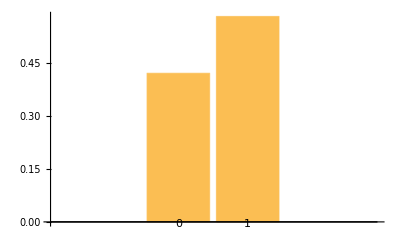

```mathematica
m1["ProbabilityPlot"]
```

```mathematica
m2=QuantumMeasurementOperator[{1,2}]@s
```

QuantumMeasurement[…]

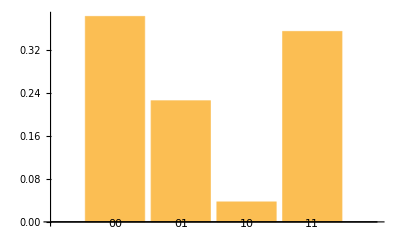

```mathematica
m2["ProbabilityPlot"]
```

```mathematica
m3=QuantumMeasurementOperator[QuantumBasis[{"X","Y"}],{1,2}]@s
```

QuantumMeasurement[…]

```mathematica
m3["Probabilities"]
```

<|ψ_(x_-)ψ_(y_-)→0.438789,ψ_(x_-)ψ_(y_+)→0.241563,ψ_(x_+)ψ_(y_-)→0.294424,ψ_(x_+)ψ_(y_+)→0.0252244|>

```mathematica
m4=QuantumMeasurementOperator[{1,2}]@QuantumState[{a,b,c,d}]
```

QuantumMeasurement[…]

```mathematica
m4["Probabilities"]
```

Association[00→Re((a Conjugate[a])/(a Conjugate[a]+b Conjugate[b]+c Conjugate[c]+d Conjugate[d])),01→Re((b Conjugate[b])/(a Conjugate[a]+b Conjugate[b]+c Conjugate[c]+d Conjugate[d])),10→Re((c Conjugate[c])/(a Conjugate[a]+b Conjugate[b]+c Conjugate[c]+d Conjugate[d])),11→Re((d Conjugate[d])/(a Conjugate[a]+b Conjugate[b]+c Conjugate[c]+d Conjugate[d]))]

```mathematica
m4["StateAssociation"]
```

```mathematica
<|00->a 00,01->b 01,10->c 10,11->d 11|>
```

#### QuantumCircuitOperator

```mathematica
QuantumCircuitOperator["Toffoli"]
```

-Graphics-

```mathematica
QuantumCircuitOperator["Toffoli"]["Operators"]
```

{QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…]}

```mathematica
QuantumCircuitOperator["Toffoli"][QuantumState["110"]]["Simplify"]
```

111

```mathematica
QuantumCircuitOperator[{QuantumOperator["H"],QuantumOperator["CNOT"]}]
```

-Graphics-

```mathematica
QuantumState[{"Register",2}]==QuantumState["00"]
```

True

```mathematica
QuantumCircuitOperator[{QuantumOperator["H"],QuantumOperator["CNOT"]}][QuantumState[{"Register",2}]]
```

00/(√2)+11/(√2)

```mathematica
QuantumCircuitOperator[{QuantumOperator["H"],QuantumOperator["CNOT"]}][QuantumState[{"Register",2}]]==QuantumState["Bell"]
```

True

```mathematica
QuantumCircuitOperator["Bell"]
```

QuantumCircuitOperator[…]

```mathematica
QuantumCircuitOperator[{"BernsteinVaziraniOracle","110"}]
```

-Graphics-

```mathematica
QuantumCircuitOperator[{"BernsteinVazirani","110"}]
```

-Graphics-

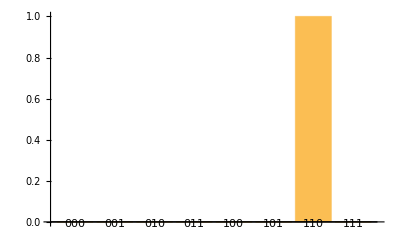

```mathematica
QuantumCircuitOperator[{"BernsteinVazirani","110"}][]["ProbabilityPlot"]
```

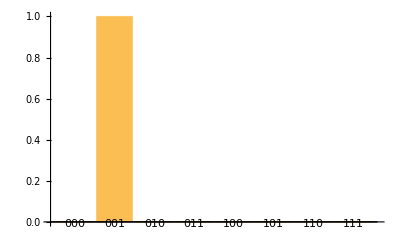

```mathematica
QuantumCircuitOperator[{"BernsteinVazirani","001"}][]["ProbabilityPlot"]
```

```mathematica
QuantumCircuitOperator[{"BooleanOracle",a&&b&&c}]
```

QuantumCircuitOperator[…]

```mathematica
SatisfiabilityInstances[a&&b&&!c,{a,b,c},All]
```

{{True,True,False}}

```mathematica
QuantumCircuitOperator[{"PhaseOracle",a&&b&&!c}][QuantumState["1100"]]
```

-1100

```mathematica
QuantumCircuitOperator[{"PhaseOracle",a&&b&&!c}][QuantumState["0010"]]
```

0010

```mathematica
QuantumCircuitOperator[{"BooleanOracle",a&&b&&!c}]@QuantumState["1100"]
```

1101

```mathematica
QuantumCircuitOperator[{"BooleanOracle",a&&b&&!c}]@QuantumState["0010"]
```

0010

```mathematica
QuantumCircuitOperator[{"Grover",a&&b&&!c}]
```

QuantumCircuitOperator[…]

```mathematica
QuantumCircuitOperator[{"Grover",a&&b&&!c}]["Flatten"]
```

QuantumCircuitOperator[…]

```mathematica
m=(QuantumCircuitOperator[{"GroverPhase",a&&b&&!c}]/*QuantumMeasurementOperator[{1,2,3}])[QuantumTensorProduct[QuantumState[{"UniformSuperposition",3}],QuantumState["0"]]]
```

QuantumMeasurement[…]

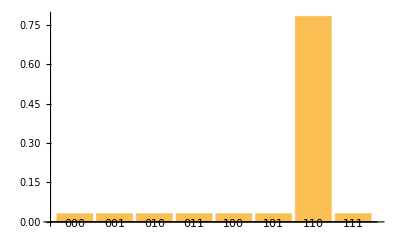

```mathematica
m["ProbabilityPlot"]
```

```mathematica
QuantumTensorProduct[QuantumOperator["H"],QuantumOperator["X"]]
```

0001/(√2)+0011/(√2)+0100/(√2)+0110/(√2)+1001/(√2)-1011/(√2)+1100/(√2)-1110/(√2)

```mathematica
QuantumCircuitOperator[{QuantumOperator["H"],QuantumOperator["X",{2}]}]
```

-Graphics-

```mathematica
QuantumCircuitOperator[{QuantumOperator["H"],QuantumOperator["X",{2}]}]["QuantumOperator"]
```

QuantumOperator[…]

```mathematica
QuantumTensorProduct[QuantumOperator["H"],QuantumOperator["X",{3}]]
```

QuantumOperator[…]

```mathematica
QuantumTensorProduct[QuantumOperator["H"],QuantumOperator["I"],QuantumOperator["X"]]
```

QuantumOperator[…]

```mathematica
QuantumOperator["RandomUnitary"]
```

QuantumOperator[QuantumState[SparseArray[Automatic, {4}, 0. + 0.*I, 
    {1, {{0, 4}, {{1}, {2}, {3}, {4}}}, {-0.6175312681304548 + 0.6336945996109875*I, 
      0.3180325948221886 - 0.3405019176682097*I, -0.2008994660756956 + 0.42038754957249047*I, 
      -0.36452089848652136 + 0.8062494820224795*I}}], 
   QuantumBasis[Association[Input -> QuditBasis[Association[{QuditName[0, Dual -> True], 1} -> 
         SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{1}}}, {1}}], 
        {QuditName[1, Dual -> True], 1} -> SparseArray[Automatic, {2}, 0, 
          {1, {{0, 1}, {{2}}}, {1}}]]], Output -> 
      QuditBasis[Association[{QuditName[0, Dual -> False], 1} -> SparseArray[Automatic, {2}, 0, 
          {1, {{0, 1}, {{1}}}, {1}}], {QuditName[1, Dual -> False], 1} -> 
         SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{2}}}, {1}}]]], Picture -> Schrödinger, 
     Label -> None, ParameterSpec -> {}]]], {{1}, {1}}]

```mathematica
List@@QuantumOperator["RandomUnitary"]
```

{QuantumState[…],{{1},{1}}}

```mathematica
List@@QuantumMeasurementOperator[]
```

{QuantumOperator[…],{1}}

```mathematica
List@@QuantumMeasurement[…]
```

{QuantumMeasurementOperator[…]}

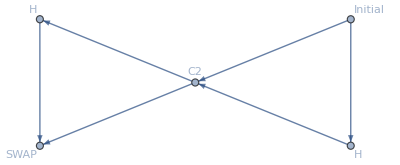

```mathematica
QuantumCircuitOperator["Fourier"]["TensorNetwork"]
```

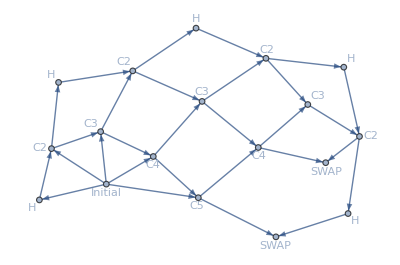

```mathematica
QuantumCircuitOperator[{"Fourier",5}]["TensorNetwork"]
```

```mathematica
QuantumCircuitOperator[{"Fourier",5}]
```

-Graphics-

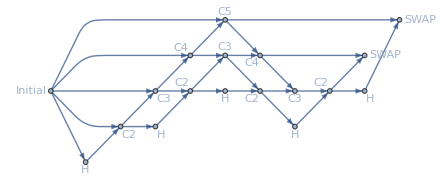

```mathematica
Graph[QuantumCircuitOperator[{"Fourier",5}]["TensorNetwork"],
GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Left}]
```

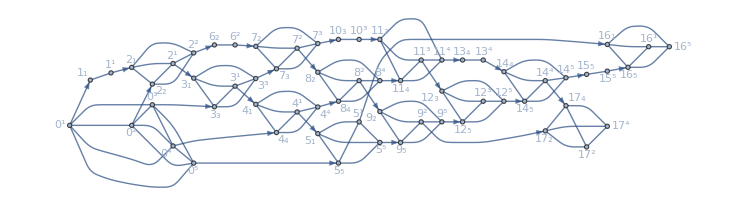

```mathematica
Graph[TensorNetworkIndexGraph@QuantumCircuitOperator[{"Fourier",5}]["TensorNetwork"],
GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Left}]
```

```mathematica
QuantumCircuitOperator[{"PhaseEstimation",QuantumOperator["RandomUnitary"]}]
```

-Graphics-

```mathematica
qiskit=QuantumCircuitOperator[{"BernsteinVazirani","0101"}]["Qiskit"]
```

QiskitCircuit[…]

```mathematica
measurement=qiskit[QuantumState["00000"]]
```

QuantumMeasurement[…]

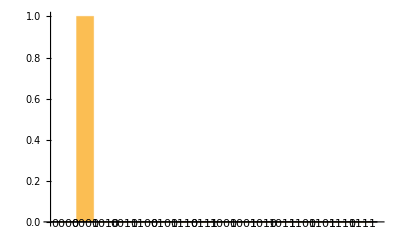

```mathematica
measurement["ProbabilityPlot"]
```

```mathematica
measurement=qiskit[QuantumState["00000"],"Provider"->"IBMQ"]
```

QuantumMeasurement[…]

```mathematica
qiskit["QASM"]
```

OPENQASM 2.0;
include "qelib1.inc";
gate i p0 {
	u3(0,0,0) p0;
}
qreg q[5];
creg c[4];
h q[0];
h q[1];
h q[2];
h q[3];
h q[4];
z q[4];
i q[0];
cx q[1],q[4];
i q[2];
cx q[3],q[4];
h q[0];
h q[1];
h q[2];
h q[3];
measure q[0] -> c[0];
measure q[1] -> c[0];
measure q[2] -> c[0];
measure q[3] -> c[0];

```mathematica
QuantumCircuitOperator[{"BernsteinVazirani","0101"}]["QASM"]
```

OPENQASM 3.0;
qubit[5] q;
bit[4] c;
U(pi/2, 0, pi) q[0];
U(pi/2, 0, pi) q[1];
U(pi/2, 0, pi) q[2];
U(pi/2, 0, pi) q[3];
U(pi/2, 0, pi) q[4];
U(0, 0, pi) q[4];
U(0, 0, pi) q[0];
ctrl(1) @ negctrl(0) @ U(pi, 0, pi) q[1] q[4];
U(0, 0, pi) q[2];
ctrl(1) @ negctrl(0) @ U(pi, 0, pi) q[3] q[4];
U(pi/2, 0, pi) q[0];
U(pi/2, 0, pi) q[1];
U(pi/2, 0, pi) q[2];
U(pi/2, 0, pi) q[3];
c[0] = measure q[0];
c[0] = measure q[1];
c[0] = measure q[2];
c[0] = measure q[3];

```mathematica
ResourceFunction["PythonVersion"][]
```

Python 3.9.1

```mathematica
ResourceFunction["PythonPackageInformation"]["qiskit"]
```

<|Name→qiskit,Version→0.36.1,Summary→Software for developing quantum computing programs,Home-page→https://github.com/Qiskit/qiskit,Author→Qiskit Development Team,Author-email→hello@qiskit.org,License→Apache 2.0,Location→/Users/swish/.pyenv/versions/3.9.1/lib/python3.9/site-packages,Requires→qiskit-aer, qiskit-ibmq-provider, qiskit-ignis, qiskit-terra,Required-by→|>

Questions please: quantum@wolfram.com

```mathematica
CloudPublish[EvaluationNotebook[],"QF_Demo.nb",Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/nikm/QF_Demo.nb]